```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
```

ColorData::notent: 116 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

```mathematica
figureNameSteadyStates2D="steady_states_2D";
figureDirectorySteadyStates2D=figureNameSteadyStates2D;
```

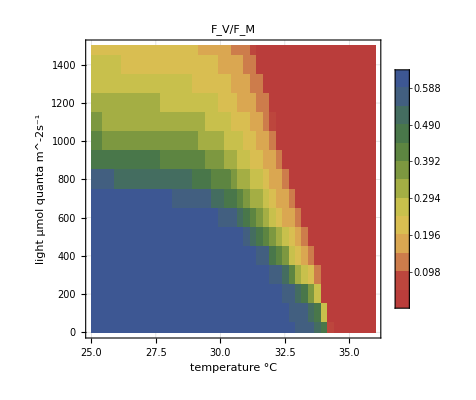

```mathematica
colorSchemes=Join[#->ColorData[{"DarkRainbow","Reverse"}]&/@{FvFm,ϕPSII},{_->ColorData["DarkRainbow"]}];
maxRanges={(*
gP->250,
gN->950,
gU->600,
ϕPSII->0.8,
FvFm->0.8,
xD->10^-6.,
c->0.75,
(*cX-> 10^-7,*)
p->26,
pX->26,
pT->26,
pD->26,
pTD->26,
n0->1.9,
n->1.9,
nX->1.9,*)
c->{0,.75},
_->Full(*Automatic*)
};
style2Dplot[quant_]:=
{LabelStyle->{14},
FrameLabel->{{"light "<>(L/.units),None},{"temperature "<>(w/.units),None}},
InterpolationOrder->0,
GridLines->Transparent,
PlotLegends->BarLegend[Automatic,LegendMarkerSize->300],
PlotRange->(quant/.maxRanges),
ImageSize->400,
ImagePadding->{{60,10},{45,10}},
Contours->12,
ColorFunction->(quant/.colorSchemes)};
makeFinalPlot[pars_,quant_,options_]:=
ListContourPlot[
Flatten[
Table[
Module[
{parsNew=Join[{w->ww,L->LL},pars]},
{ww,LL,quant/.finalState[parsNew]/.parsNew}
],
{ww,25,36,.25},
{LL,0,1500,100(*25*)}
],
1],
Evaluate@options,
Evaluate@style2Dplot[quant]
];
(Export[NotebookDirectory[]<>"export/steady-state-2D-FvFm-start-healthy.pdf",#/. {_EdgeForm,c_?ColorQ,rest__}:>{EdgeForm[Directive[Thin,c]],c,rest}];#)&@(makeFinalPlot[Join[{tmax-> 24 3600},pars[4]],#,{(*ColorFunction->ColorData[{"DarkRainbow","Reverse"}],*)PlotLabel->(#/.names)}])&@FvFm
```

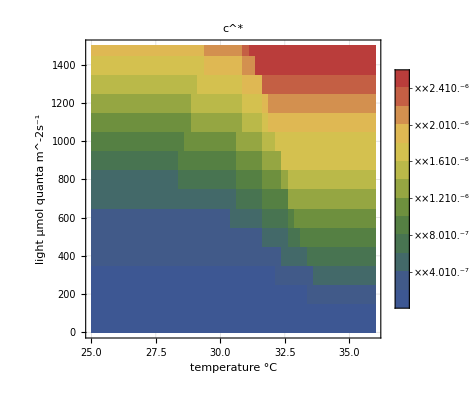
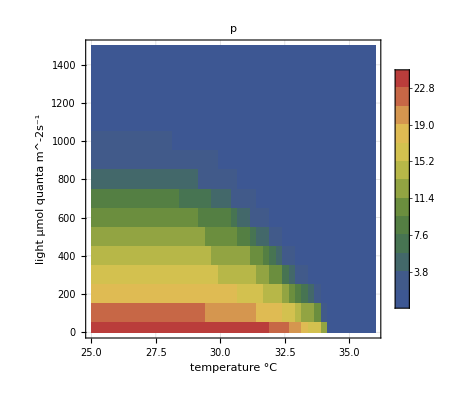
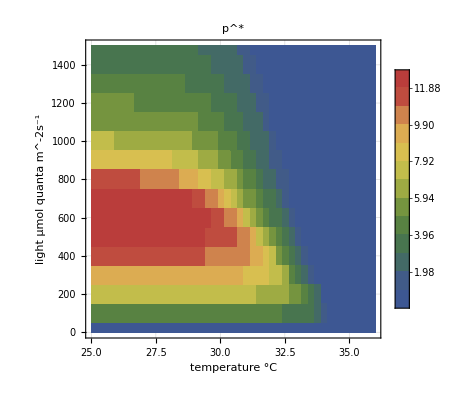
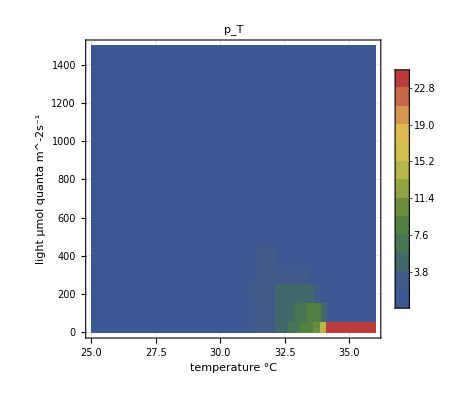
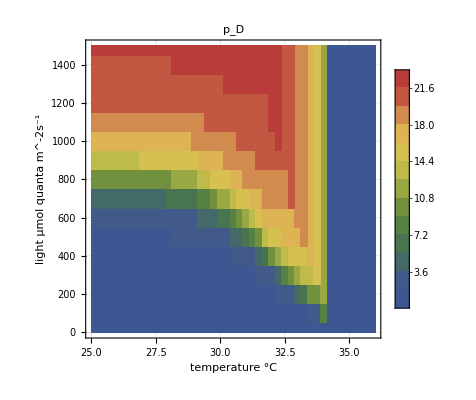
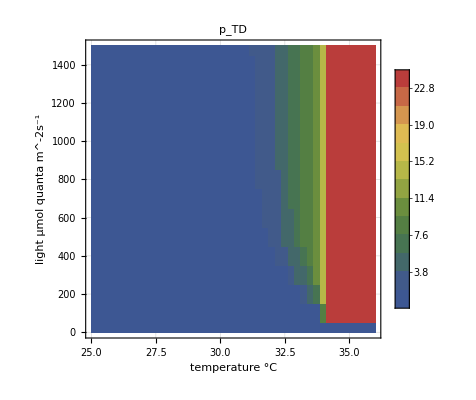
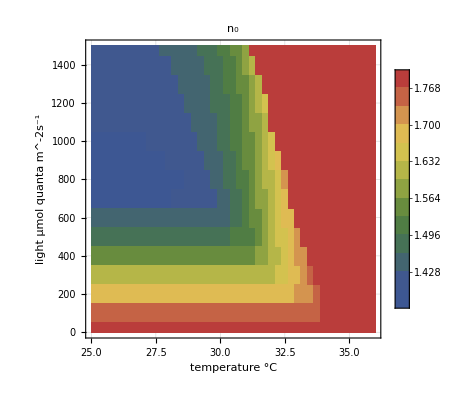
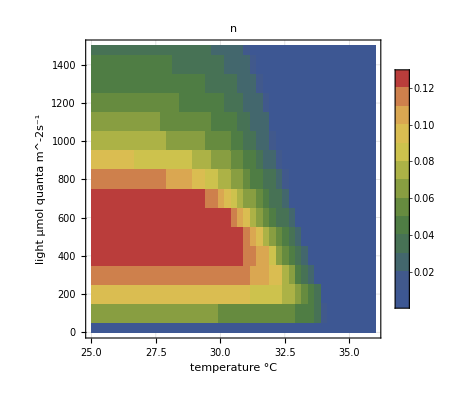

```mathematica
(Export[NotebookDirectory[]<>"export/"<>figureDirectorySteadyStates2D<>"/"<>figureNameSteadyStates2D<>".pdf",#/. {_EdgeForm,c_?ColorQ,rest__}:>{EdgeForm[Directive[Thin,c]],c,rest}];#)&@GridMap[makeFinalPlot[Join[{tmax->24 3600},pars[6]],#,{PlotLabel->#/.names}]&,quants/.c->Nothing,Spacer[30],{Spacings->0}]
```